```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\daisy\OneDrive - University of Cape Town\0. Masters Project\Amplitude Coefficient calculations

```mathematica
TesttMax=20;
TesttPts=300;
TestPrec=100;
TesttVals = Table[N[TesttMax*(i)/(TesttPts), TestPrec], {i, 1, TesttPts}];
```

```mathematica
AmplitudeCoefficientTest1[as_,Bs_,ReturnAmp_,tVals_,Prec_]:=Module[{bs,ϕPts,NNND,NNNDTab,Genf,FtoNSwap,ϕt,cc,PTab},
bs=Bs[[1+LengthWhile[Bs,#==0&];;-1-LengthWhile[Reverse@Bs,#==0&]]]; (*removes tail of zeros and initial zeros*)
 ϕPts = Length[bs];
(*"Here the derivatives are computed at the time-points.  "*)
	 NNND[0] = ReturnAmp;
	Do[NNND[j+1] =  D[NNND[j], t]    , {j, 0, ϕPts}  ];//EchoTiming;
	NNNDTab = Table[NNND[j]/.t->tVals, {j, 0, ϕPts}];//EchoTiming;
	Genf=F[t];
	(*"The substitution to the function F(t)"*)
	FtoNSwap = Table[D[F[t], {t,k}] -> NNNDTab[[k+1]], {k, 0, ϕPts}];
	 ϕt = Table[D[ Genf  , {t, k}], {k, 0, ϕPts}]/.FtoNSwap;
	(* Echo[Table[Precision[NNND[i]],{i,0, ϕPts}]];*)
(*"Here we compute the coefficeints cc "*)
	Clear[cc];   cc[0,0]=1; cc[0,-1] = 0;
(*CHANGED TO HAVE N ONLY GO TO ϕPts-1*)
Do[  cc[m,n+1]  = N[(If[m≥ 1, I*cc[m-1,n], 0]  +If[m≤ n, as[[n+1]]*cc[m,n], 0]   - If[m≤n -1&& n>0, bs[[n]]*cc[m,n-1] , 0 ])/bs[[n+1]], Prec]  , {n, 0, ϕPts-1}, {m, 0, n+1}]//EchoTiming; 
PTab = Table[  Sum[ N[N[cc[m,kk], Prec]*ϕt[[m+1]], Prec], {m, 0, kk}] , {kk, 0, ϕPts}]//EchoTiming]
```

```mathematica
AmplitudeCoefficientTest2[as_,Bs_,ReturnAmp_,tVals_,Prec_]:=Module[{bs,ϕPts,NNND,NNNDTab,Genf,FtoNSwap,ϕt,cc,PTab},
bs=Bs[[1+LengthWhile[Bs,#==0&];;-1-LengthWhile[Reverse@Bs,#==0&]]]; (*removes tail of zeros and initial zeros*)
 ϕPts = Length[bs];
(*"Here the derivatives are computed at the time-points.  "*)
	 NNND[0] = ReturnAmp;
	Do[NNND[j+1] =  D[NNND[j], t]    , {j, 0, ϕPts}  ];//EchoTiming;
	NNNDTab = Table[NNND[j]/.t->tVals, {j, 0, ϕPts}];//EchoTiming;
(*"Here we compute the coefficeints cc "*)
Clear[cc];   cc[0,0]=1; cc[0,-1] = 0;
(*CHANGED TO HAVE N ONLY GO TO ϕPts-1*)
Do[  cc[m,n+1]  = N[(If[m≥ 1, I*cc[m-1,n], 0]  +If[m≤ n, as[[n+1]]*cc[m,n], 0]   - If[m≤n -1&& n>0, bs[[n]]*cc[m,n-1] , 0 ])/bs[[n+1]], Prec]  , {n, 0, ϕPts-1}, {m, 0, n+1}]//EchoTiming; 
PTab = Table[  Sum[ N[N[cc[m,kk], Prec]*NNNDTab[[m+1]], Prec], {m, 0, kk}] , {kk, 0, ϕPts}]//EchoTiming]
```

```mathematica
AmplitudeCoefficientTest3[as_,Bs_,ReturnAmp_,tVals_,Prec_]:=Module[{bs,ϕPts,NNND,NNNDTab,Genf,FtoNSwap,ϕt,cc,PTab},
bs=Bs[[1+LengthWhile[Bs,#==0&];;-1-LengthWhile[Reverse@Bs,#==0&]]]; (*removes tail of zeros and initial zeros*)
 ϕPts = Length[bs];
(*"Here the derivatives are computed at the time-points.  "*)
	 NNND[0] = Chop[Simplify@ExpToTrig[ReturnAmp],10^-30];
	Do[NNND[j+1] =  D[NNND[j], t]    , {j, 0, ϕPts}  ];//EchoTiming;
	NNNDTab = Table[NNND[j]/.t->tVals, {j, 0, ϕPts}];//EchoTiming;
(*"Here we compute the coefficeints cc "*)
Clear[cc];   cc[0,0]=1; cc[0,-1] = 0;
(*CHANGED TO HAVE N ONLY GO TO ϕPts-1*)
Do[  cc[m,n+1]  = N[(If[m≥ 1, I*cc[m-1,n], 0]  +If[m≤ n, as[[n+1]]*cc[m,n], 0]   - If[m≤n -1&& n>0, bs[[n]]*cc[m,n-1] , 0 ])/bs[[n+1]], Prec]  , {n, 0, ϕPts-1}, {m, 0, n+1}]//EchoTiming; 
PTab = Table[  Sum[ N[N[cc[m,kk], Prec]*NNNDTab[[m+1]], Prec], {m, 0, kk}] , {kk, 0, ϕPts}]//EchoTiming]
```

```mathematica
AmplitudeCoefficientTest4[as_,Bs_,ReturnAmp_,tVals_,Prec_]:=Module[{bs,ϕPts,NNND,NNNDTab,Genf,FtoNSwap,ϕt,cc,PTab},
bs=Bs[[1+LengthWhile[Bs,#==0&];;-1-LengthWhile[Reverse@Bs,#==0&]]]; (*removes tail of zeros and initial zeros*)
 ϕPts = Length[bs];
(*"Here the derivatives are computed at the time-points.  "*)
	 NNND[0] = Chop[Simplify@ExpToTrig[ReturnAmp],10^-30];
	Do[NNND[j+1] =  D[NNND[j], t]    , {j, 0, ϕPts}  ];//EchoTiming;
	NNNDTab = Table[NNND[j]/.t->tVals, {j, 0, ϕPts}];//EchoTiming;
(*"Here we compute the coefficeints cc "*)
Clear[cc];   cc[0,0]=1; cc[0,-1] = 0;
(*CHANGED TO HAVE N ONLY GO TO ϕPts-1*)
Do[  cc[m,n+1]  = (If[m≥ 1, I*cc[m-1,n], 0]  +If[m≤ n, as[[n+1]]*cc[m,n], 0]   - If[m≤n -1&& n>0, bs[[n]]*cc[m,n-1] , 0 ])/bs[[n+1]]  , {n, 0, ϕPts-1}, {m, 0, n+1}]//EchoTiming; 
PTab = Table[  Sum[ N[cc[m,kk]*NNNDTab[[m+1]], Prec], {m, 0, kk}] , {kk, 0, ϕPts}]//EchoTiming]
```

```mathematica
AmplitudeCoefficientTest5[as_,Bs_,ReturnAmp_,tVals_,Prec_]:=Module[{bs,ϕPts,NNND,NNNDTab,Genf,FtoNSwap,ϕt,cc,PTab},
bs=Bs[[1+LengthWhile[Bs,#==0&];;-1-LengthWhile[Reverse@Bs,#==0&]]]; (*removes tail of zeros and initial zeros*)
 ϕPts = Length[bs];
(*"Here the derivatives are computed at the time-points.  "*)
	 NNND[0] = ReturnAmp;
(*	Do[NNND[j+1] =  D[NNND[j], t]    , {j, 0, ϕPts}  ];//EchoTiming;*)
NNND=NestList[D[#,t]&,ReturnAmp,ϕPts];//EchoTiming;
	NNNDTab = Table[NNND[[j]]/.t->tVals, {j, 0, ϕPts}];//EchoTiming;
(*"Here we compute the coefficeints cc "*)
Clear[cc];   cc[0,0]=1; cc[0,-1] = 0;
(*CHANGED TO HAVE N ONLY GO TO ϕPts-1*)
Do[  cc[m,n+1]  = N[(If[m≥ 1, I*cc[m-1,n], 0]  +If[m≤ n, as[[n+1]]*cc[m,n], 0]   - If[m≤n -1&& n>0, bs[[n]]*cc[m,n-1] , 0 ])/bs[[n+1]], Prec]  , {n, 0, ϕPts-1}, {m, 0, n+1}]//EchoTiming; 
PTab = Table[  Sum[ cc[m,kk]*NNNDTab[[m+1]], {m, 0, kk}] , {kk, 0, ϕPts}]//EchoTiming]
```

```mathematica
{RetAmpJacoL6sp1, RetAmpJacoL6sp2, RetAmpJacoL6sp3, RetAmpJacoL6sp4}=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Return Amplitudes\\ReturnAmpJacoL6TFIMcd1234.txt"]];
```

```mathematica
bsL6sp1=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Lanczos Coefficients\\bs_Lanczos_HPC_L6_cdMode1.txt","Table", HeaderLines->2][[2]];
asL6sp1=Table[0,Length[bsL6sp1]];
```

```mathematica
bsL6sp2=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Lanczos Coefficients\\bs_Lanczos_HPC_L6_spMode2.txt","Table", HeaderLines->2][[2]];
asL6sp2=Table[0,Length[bsL6sp2]];
```

```mathematica
bsL6sp3=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Lanczos Coefficients\\bs_Lanczos_HPC_L6_spMode3.txt","Table", HeaderLines->2][[2]];
asL6sp3=Table[0,Length[bsL6sp3]];
```

```mathematica
bsL7cd1=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Lanczos Coefficients\\bs_Lanczos_HPC_L7_cdMode1.txt","Table", HeaderLines->2][[2]];
asL7cd1=Table[0,Length[bsL7cd1]];
```

```mathematica
{RetAmpJacoL7cd1, RetAmpJacoL7cd2, RetAmpJacoL7cd3, RetAmpJacoL7cd4}=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Return Amplitudes\\ReturnAmpJacoL7TFIMcd1234.txt"]];
```

```mathematica
PTabFrac2=AmplitudeCoefficientTest2[asL7cd1,bsL7cd1,RetAmpJacoL7cd1,TesttVals,TestPrec];//EchoTiming
```

0.0004422

8.25071

0.0243746

0.536498

8.87692

```mathematica
PTabFrac3=AmplitudeCoefficientTest3[asL7cd1,bsL7cd1,RetAmpJacoL7cd1,TesttVals,TestPrec];//EchoTiming
```

0.0050536

2.78396

0.0238738

0.342268

3.20778

```mathematica
PTabFrac4=AmplitudeCoefficientTest4[asL7cd1,bsL7cd1,RetAmpJacoL7cd1,TesttVals,TestPrec];//EchoTiming
```

0.0033231

2.76026

0.0294573

0.336498

3.18722

```mathematica
Length[bsL7cd1]
```

73

```mathematica
Info="Some info about generating the probability amplitudes";
Info2= "We need to know the Lanczos coeffs, their precision, the Return amplitudes, and its precision, the tVals used, and the working precision for the amplitude coefficient calculation";
```

```mathematica
Export["Test_ProbAmp_output.m.gz", {Info,Info2,PTabFrac2}]//AbsoluteTiming
```

{0.744405,Test_ProbAmp_output.m.gz}

```mathematica
Export["Test_ProbAmp_output.m", {Info,Info2,PTabFrac2}]//AbsoluteTiming
```

{0.531846,Test_ProbAmp_output.m}

```mathematica
PTabFrac2[[1,1]]
```

0.986719232468043841245529559441875381465253359143112900234121559055653958128432213439019930402655393+0. ⅈ

```mathematica
PTabFrac2Imported=Import["Test_ProbAmp_output.m.gz"];//AbsoluteTiming
```

{0.379417,Null}

```mathematica
FileByteCount["Test_ProbAmp_output.m.gz"]
```

1531264

```mathematica
FileByteCount["Test_ProbAmp_output.m"]
```

3417304

```mathematica
PTabFrac2Imported=Import["Test_ProbAmp_output.m"];//AbsoluteTiming
```

{0.343377,Null}

```mathematica
PTabFrac2Imported[[3]]
```

{{0.986719232468043841245529559441875381465253359143112900234121559055653958128432213439019930402655393+0. ⅈ,0.947502512689392373520303416121912733447233710863165686739996845937376678967798679492192340717500609+0. ⅈ,296,-0.1515378983329623072389455979631239280536975054629881076900731792467742835904562877217488820802049+0. ⅈ,-0.1780457295996573722130750633912459140511971403846268461696890242683871817226881185336167826371731+0. ⅈ},71,{1}}
 |  |  |  |

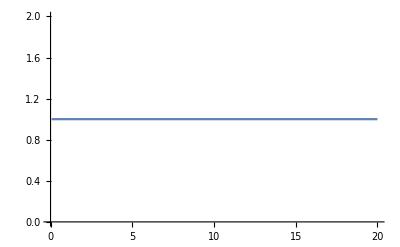

```mathematica
pPlot=Table[{TesttVals[[j]],Sum[Abs[PTabFrac4[[k,j]]^2],{k,1,73}]},{j,1,Length[TesttVals]}];
ListLinePlot[pPlot]
```

```mathematica
pPlot=Table[{TesttVals[[j]],Sum[Abs[PTabFrac3[[k,j]]^2],{k,1,73}]},{j,1,Length[TesttVals]}];
ListLinePlot[pPlot]
```

-Graphics-

```mathematica
Table[Precision[PTabFrac3[[k,300]]], {k,1,73}]
```

{97.8296,97.6045,97.5379,97.0363,97.1426,96.3006,96.4796,95.4582,95.9016,95.3958,95.3006,94.7626,94.1283,93.7979,94.0727,93.0862,93.686,92.6661,93.1694,92.7647,92.4905,92.2996,90.5955,89.8903,91.5458,91.2551,90.9602,90.7964,90.0329,89.9653,88.462,88.4504,88.092,88.0777,87.6212,87.3564,86.8365,85.6678,85.3625,84.5483,84.1802,83.7594,82.8233,83.4234,82.7387,82.2493,81.5513,81.5073,81.0132,80.0388,79.4883,78.9285,78.7518,78.3204,77.6227,76.5602,76.2571,75.7087,75.2955,73.9514,73.7564,72.9849,71.8719,70.3851,69.8164,68.492,68.6763,67.0379,64.6314,65.909,62.5023,61.849,61.5974}

```mathematica
Table[Precision[PTabFrac4[[k,300]]], {k,1,73}]
```

{97.8296,97.6063,97.5418,97.0376,97.1466,96.3015,96.4833,95.4588,95.9048,95.3963,95.3031,94.7631,94.1302,93.7985,94.0744,93.0868,93.6876,92.6668,93.1712,92.7655,92.4926,92.3004,90.598,89.8912,91.5485,91.256,90.9631,90.7974,90.0359,89.9663,88.465,88.4516,88.095,88.0789,87.6242,87.3578,86.8394,85.6693,85.3653,84.5499,84.1829,83.7612,82.8259,83.4253,82.7412,82.2512,81.5537,81.5092,81.0156,80.0407,79.4906,78.9304,78.7541,78.3222,77.6249,76.5619,76.2594,75.7103,75.2977,73.9528,73.7587,72.9861,71.8742,70.3861,69.8188,68.4929,68.6788,67.0386,64.634,65.9094,62.5049,61.8494,61.6001}

```mathematica
Manipulate[ListLinePlot[Table[Abs[PTabFrac3[[k,tt]]]^2,{k,1,73}], PlotRange->{0,1}],{tt,0,300,1}]
```

## Line-by-line

```mathematica
Precision[bsL7cd1[[2]]]
```

999.389

```mathematica
Precision[RetAmpJacoL7cd1]
```

250.493

```mathematica
Bs=bsL7cd1;ReturnAmp=RetAmpJacoL7cd1;as=ConstantArray[0,Length[Bs]];
```

```mathematica
(*ReturnAmpChop=Chop[FullSimplify[RetAmpJacoL6sp1]];*)
```

```mathematica
bs=Bs[[1+LengthWhile[Bs,#==0&];;-1-LengthWhile[Reverse@Bs,#==0&]]]; (*removes tail of zeros and initial zeros*)
 ϕPts = Length[bs]
(*"Here the derivatives are computed at the time-points.  "*)
```

72

```mathematica
Chop@FullSimplify@ReturnAmp
```

```mathematica
NNND[0]=ReturnAmp;
```

```mathematica
NNND[0] =Chop@Simplify@ExpToTrig[ReturnAmp];
```

```mathematica
(*ReturnAmp is an algebraic expression in terms of t*)
Do[NNND[j+1] =  D[NNND[j], t]    , {j, 0, ϕPts}  ];//EchoTiming(*take derivatives of the return amplitude Length[bs] times*)
```

0.000428

```mathematica
NNND=NestList[D[#,t]&,ReturnAmp,ϕPts];//EchoTiming;
```

0.0271735

```mathematica
NNNDTab = Table[NNND[j]/.t->TesttVals, {j, 0, ϕPts}];//EchoTiming; (*evaluate the derivatives on all the tvals*)
```

8.97637

```mathematica
Precision[NNND[4]/.t->TesttVals[[1]]]
```

100.604

```mathematica
NNNDTab = ParallelTable[NNND[j]/.t->TesttVals, {j, 0, ϕPts}, Method->"CoarsestGrained"];//EchoTiming;
Table[Precision[NNNDTab[[i]]],{i,1,70}]
```

3.19943

{15.9355,15.8547,16.0019,15.7859,14.882,13.9819,14.3178,14.9056,15.3241,15.1484,14.922,14.7327,14.9931,15.1024,14.2079,14.7879,14.1614,14.7269,14.2324,14.4146,14.7109,14.6502,14.0224,15.0279,15.3673,14.8046,16.0277,15.6581,15.0267,14.5087,15.0001,14.9312,15.5969,15.8227,15.7232,15.4436,15.14,15.948,15.0973,15.1048,15.0369,14.8857,14.8742,14.5979,15.6999,15.8724,15.1799,14.1344,15.5504,15.5463,14.7136,15.3588,15.3012,14.4012,15.7384,15.5036,14.8225,15.7291,15.5512,15.3864,15.612,15.5392,15.6484,15.6727,15.6531,15.7009,14.8067,16.1246,15.4674,15.004}

```mathematica
NNNDTab = Table[NNND[j]/.t->TesttVals, {j, 0, ϕPts}];//EchoTiming;
Table[Precision[NNNDTab[[i]]],{i,1,70}]
```

9.80988

{95.9355,95.8547,96.0019,95.7859,94.882,93.9819,94.3178,94.9056,95.3241,95.1484,94.922,94.7327,94.9931,95.1024,94.2079,94.7879,94.1614,94.7269,94.2324,94.4146,94.7109,94.6502,94.0224,95.0279,95.3673,94.8046,96.0277,95.6581,95.0267,94.5087,95.0001,94.9312,95.5969,95.8227,95.7232,95.4436,95.14,95.948,95.0973,95.1048,95.0369,94.8857,94.8742,94.5979,95.6999,95.8724,95.1799,94.1344,95.5504,95.5463,94.7136,95.3588,95.3012,94.4012,95.7384,95.5036,94.8225,95.7291,95.5512,95.3864,95.612,95.5392,95.6484,95.6727,95.6531,95.7009,94.8067,96.1246,95.4674,95.004}

```mathematica
16*Log[2,10]//N
```

53.1508

```mathematica
TesttVals = N[Table[TesttMax*(i)/(TesttPts), {i, 1, TesttPts}], 100];
```

```mathematica
TestList= Table[N[TesttMax*(i)/(TesttPts),100], {i, 1, TesttPts}];
```

```mathematica
PiList2=N[Table[N[Pi,40],{i,3,30}],20];
```

```mathematica
ParallelTable[t+2/.t->TesttVals,{i,3,10}]
```

```mathematica
Table[t+2/.t->TesttVals,{i,3,30}]
```

{{2.0666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667,2.1333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333,2.2,294,21.86666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667,21.93333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333,22.},26,{136,298,22.}}
 |  |  |  |

```mathematica
Clear[cc];   cc[0,0]=1; cc[0,-1] = 0;
(*CHANGED TO HAVE N ONLY GO TO ϕPts-1*)
Do[  cc[m,n+1]  = N[(If[m≥ 1, I*cc[m-1,n], 0]  +If[m≤ n, as[[n+1]]*cc[m,n], 0]   - If[m≤n -1&& n>0, bs[[n]]*cc[m,n-1] , 0 ])/bs[[n+1]], TestPrec]  , {n, 0, ϕPts-1}, {m, 0, n+1}]//EchoTiming;
```

0.0238434

```mathematica
PTab = Table[  Sum[ N[N[cc[m,kk], TestPrec]*NNNDTab[[m+1]], TestPrec], {m, 0, kk}] , {kk, 0, ϕPts}]//EchoTiming; 
(*Precision drops as first index increases*)
(**)
```

0.442005

```mathematica
Table[PTab[[42,i]],{i,0,ϕPts}]
```

{List,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-2.×10^-6 ⅈ,0.-4.×10^-6 ⅈ,0.-6.×10^-6 ⅈ,0.-0.00001 ⅈ,0.-0.00002 ⅈ,0.-0.00003 ⅈ,0.-0.00004 ⅈ,0.-0.00006 ⅈ,0.-0.0001 ⅈ,0.-0.00015 ⅈ,0.-0.00022 ⅈ,0.-0.00033 ⅈ,0.-0.00049 ⅈ}

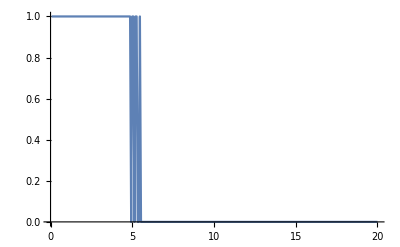

```mathematica
PTabPlot=Table[{TesttVals[[j]],Sum[Abs[PTab[[k,j]]^2],{k,1,53}]},{j,1,Length[TesttVals]}];
ListLinePlot[PTabPlot]
```

## Converting derivative to replacement rule

```mathematica
DerivSwap =  β_ Exp[α_*t]:> β α*Exp[α*t];
```

```mathematica
ConstantZero=Plus[β_?NumericQ,m_]:>m;
```

```mathematica
NewZero=c_?NumericQ :> 0
```

c_?NumericQ:>0

```mathematica
NewZero2=c_?NumericQ/;Head[c]===Symbol:>0
```

c_?NumericQ/;Head[c]===Symbol:>0

```mathematica
expr=3 x^2+2 x-5+Exp[0.983 x]+y^3-7 z;
```

```mathematica
Testexpr=Plus[0.7,t,233t,Exp[Plus[405*I*t,5]]];
```

```mathematica
Longexpr=23 Exp[9.3456789234567*I*t] + 230+17 Exp[0.4656789234567*I*t]+23 Exp[9.34456789234567*I*t] + 230+17 Exp[0.4567829234567*I*t]+23 Exp[9.34567589234567*I*t] + 230+17 Exp[0.4567896234567*I*t]+23 Exp[9.34561789234567*I*t] + 230+17 Exp[0.4567899234567*I*t]+23 Exp[9.34567879234567*I*t] + 230+17 Exp[0.4567889234567*I*t];
```

```mathematica
Testexpr/.ConstantZero
```

ⅇ^(5+405 ⅈ t)+234 t

```mathematica
Testexpr/.NewZero2
```

0.7+0^(5+405 ⅈ t)+234 t

```mathematica
Longexpr/.DerivSwap/.ConstantZero
```

(0.+7.76531 ⅈ) ⅇ^((0.+0.456783 ⅈ) t)+(0.+7.76541 ⅈ) ⅇ^((0.+0.456789 ⅈ) t)+(0.+7.76542 ⅈ) ⅇ^((0.+0.45679 ⅈ) t)+(0.+7.76543 ⅈ) ⅇ^((0.+0.45679 ⅈ) t)+(0.+7.91654 ⅈ) ⅇ^((0.+0.465679 ⅈ) t)+(0.+214.925 ⅈ) ⅇ^((0.+9.34457 ⅈ) t)+(0.+214.949 ⅈ) ⅇ^((0.+9.34562 ⅈ) t)+(0.+214.951 ⅈ) ⅇ^((0.+9.34568 ⅈ) t)+(0.+214.951 ⅈ) ⅇ^((0.+9.34568 ⅈ) t)+(0.+214.951 ⅈ) ⅇ^((0.+9.34568 ⅈ) t)

```mathematica
result=expr/. {c_?NumericQ/;Head[c]===Symbol:>0}
```

-5+0^(0.983 x)+2 x+3 x^2+y^3-7 z

```mathematica
result = expr /. {c_?NumericQ /; FreeQ[c, _Symbol] :> 0}
```

2

```mathematica
result = expr /. {c_?NumericQ /; Head[c]===Integer:>"weird"}
```

weird+ⅇ^(0.983 x)+weird x+weird x^weird+y^weird+weird z

```mathematica
list=Level[expr,1]
```

{-5,ⅇ^(0.983 x),2 x,3 x^2,y^3,-7 z}

```mathematica
heads=Table[Head[Level[expr,1][[i]]],{i,1,6}]
```

{Integer,Power,Times,Times,Power,Times}

```mathematica
Nums=Table[NumericQ[list[[i]]],{i,1,6}]
```

{True,False,False,False,False,False}

```mathematica
a=0.12345678912345678912345;α=2.111111111111111111111;
NewExpr=a*Exp[I*α*t];
```

```mathematica
Clear[p];
p[0]=NewExpr;
Do[p[i+1]=D[p[i], t];,{i, 0, 20} ];
p[20]//FullForm
```

Times[381712.87423009677573,Power[E,Times[Complex[0,2.11111111111111111111],t]]]

```mathematica
D[NewExpr,{t,20}]//FullForm
```

Times[381712.87423009677573,Power[E,Times[Complex[0,2.11111111111111111111],t]]]

```mathematica
(I*α)^20*NewExpr//FullForm
```

Times[381712.87423009677573,Power[E,Times[Complex[0,2.11111111111111111111],t]]]

```mathematica
KroneckerProduct[PauliMatrix[3],IdentityMatrix[2],PauliMatrix[3]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
KroneckerProduct[PauliMatrix[3],IdentityMatrix[2],IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],PauliMatrix[3]]//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2)

```mathematica
p1=PauliMatrix[1];p2=PauliMatrix[2];p3=PauliMatrix[3];id=IdentityMatrix[2];
OpList={p3,id,p3};
Apply[KroneckerProduct,OpList]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## su2 Tests

```mathematica
Get["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude_Coefficient_Package.wl"]
```

```mathematica
tMax=5;
tPts=100;
Prec=40;
tVals = N[Table[tMax*(i)/(tPts), {i, 1, tPts}], Prec];
```

```mathematica
α=1;j=10;
su2bs=Table[α*Sqrt[n(2*j-n+1)],{n,0,20}];su2as=ConstantArray[0,Length[su2bs]];Length[su2as]
```

21

```mathematica
su2RetAmp=1/Cos[α*t]^(-2*j)
```

Cos[t]^20

```mathematica
N[su2bs]
```

{0.,4.47214,6.16441,7.34847,8.24621,8.94427,9.48683,9.89949,10.198,10.3923,10.4881,10.4881,10.3923,10.198,9.89949,9.48683,8.94427,8.24621,7.34847,6.16441,4.47214}

```mathematica
su2AC=AmplitudeCoefficient[su2as,su2bs,su2RetAmp,tVals,Prec];
```

0.0002812

0.106824

0.0026702

0.0095369

```mathematica
su2AC[[2,1]]
```

-0.218265571308255034194367009769180808294 ⅈ

```mathematica
Abs[su2AC[[20,1]]^2]
```

7.143763511×10^-49

```mathematica
Trunc=10;
MinBound=Table[{tVals[[j]],(Trunc)*(1-Sum[Abs[su2AC[[k,j]]^2],{k,1,Trunc}])},{j,1,Length[tVals]}];
MaxKrylovBound=Table[{tVals[[j]],21*(1-Sum[Abs[su2AC[[k,j]]^2],{k,1,Trunc}])},{j,1,Length[tVals]}];
```

```mathematica
Ks=Table[{tVals[[j]],Sum[(k-1)*Abs[su2AC[[k,j]]^2],{k,1,21}]},{j,1,Length[tVals]}];
KsTrunc=Table[{tVals[[j]],Sum[(k-1)*Abs[su2AC[[k,j]]^2],{k,1,Trunc}]},{j,1,Length[tVals]}];
Kdiff=Table[{tVals[[j]],Sum[(k-1)*Abs[su2AC[[k,j]]^2],{k,1,21}]-Sum[(k-1)*Abs[su2AC[[k,j]]^2],{k,1,Trunc}]},{j,1,Length[tVals]}];
```

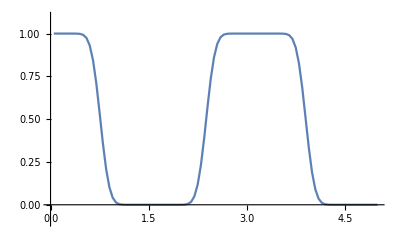

```mathematica
ProbAmpsTrunc=Table[{tVals[[j]],Sum[Abs[su2AC[[k,j]]^2],{k,1,Trunc}]},{j,1,Length[tVals]}];
ListLinePlot[ProbAmpsTrunc, PlotRange->{-0.1,1.1}]
```

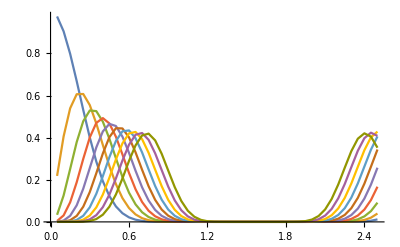

```mathematica
ϕs=Table[Table[{tVals[[j]],Abs[su2AC[[k,j]]]},{j,1,50}],{k,1,10}];
ListLinePlot[ϕs, PlotRange->All]
```

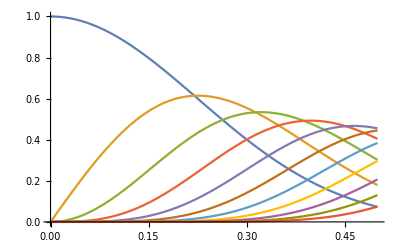

```mathematica
ϕtab=Table[(Sqrt[Gamma[2*j+1]/(Factorial[n]*Gamma[2*j-n+1])])*(Tan[α*t]^n)/(Cos[α*t]^(-2*j)),{n,0,10}];
Plot[ϕtab,{t,0,0.5}, PlotRange->All]
```

```mathematica
Series[ϕtab[[3]],{t,0,5}]
```

√190 t^2-(28 √190 t^4)/3+O[t]^6

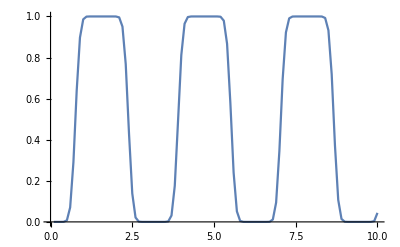

```mathematica
Eps0=Table[{tVals[[j]],(1-Sum[Abs[su2AC[[k,j]]^2],{k,1,Trunc}])},{j,1,Length[tVals]}];
Eps0interp=Interpolation[Eps0,Method->"Spline"][t];
(*Plot[Eps0interp,{0,10}]*)
```

```mathematica
a=D[Eps0interp,t]
```

InterpolatingFunction[…][t]

```mathematica
MaxBoundFn=0.5*t*Abs[D[Eps0interp,t]];
```

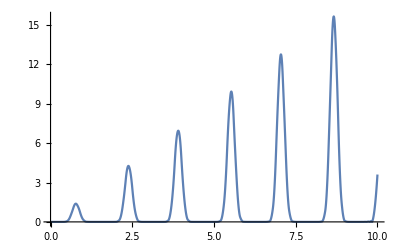

```mathematica
Plot[MaxBoundFn,{t,0,10},PlotRange->All]
```

```mathematica
MaxBound=Table[{tVals[[j]],(MaxBoundFn/.t->tVals)[[j]]},{j,1,Length[tVals]}];
```

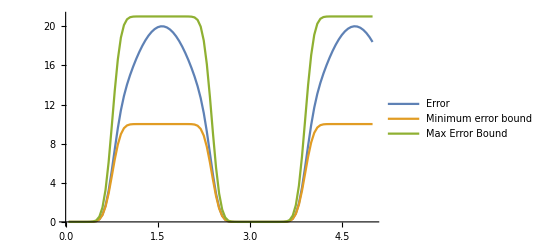

```mathematica
ListLinePlot[{Kdiff,MinBound,MaxKrylovBound}, PlotLegends->{"Error", "Minimum error bound", "Max Error Bound"}, PlotRange->All]
```

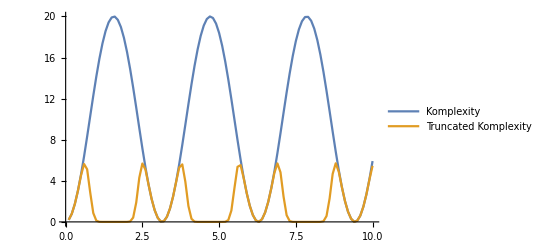

```mathematica
ListLinePlot[{Ks,KsTrunc}, PlotLegends->{"Komplexity", "Truncated Komplexity"}]
```

```mathematica
16/500
```

4/125

```mathematica
Manipulate[ListLinePlot[Table[Abs[su2AC[[k,tt]]]^2,{k,1,21}], PlotRange->{0,1}],{tt,0,100,1}]
```

Part::partd: Part specification su2AC⟦1,88⟧ is longer than depth of object.

Part::partd: Part specification su2AC⟦2,88⟧ is longer than depth of object.

Part::partd: Part specification su2AC⟦3,88⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
ϕs=Table[Table[su2AC[[k,j]],{j,1,Length[tVals]}],{k,1,21}];
ϕstars=Table[Table[{tVals[[j]],Conjugate[su2AC[[k,j]]]},{j,1,Length[tVals]}],{k,1,21}];
```

```mathematica
ϕsInterp=Table[Interpolation[ϕs[[i]],Method->"Spline"][t],{i,1,21}];
```

Interpolation::mspl: The Spline method could not be used because the data could not be coerced to machine real numbers.

General::stop: Further output of Interpolation::mspl will be suppressed during this calculation.

```mathematica
ϕs[[2]]
```

{-0.218265571308255034194367009769180808294 ⅈ,-0.405942020741433834871712743535653646418 ⅈ,-0.539256969373048158297160594807546787074 ⅈ,-0.606040755513681303598504427029423362049 ⅈ,-0.607194171076779580303004361963887673012 ⅈ,-0.554719116892059780122978659942527773643 ⅈ,-0.467305159430968884340345343925720044727 ⅈ,-0.36509915353359701099744070130938430977 ⅈ,-0.265262425002868161198223935710469967641 ⅈ,-0.179352682551697362539470511179743721558 ⅈ,-0.112768448436084539927889957783309745033 ⅈ,-0.065806634282216571990186656663852201803 ⅈ,-0.035532117214098717205607499984584912118 ⅈ,-0.017677160438608312073524664405599298333 ⅈ,-0.0080588262295354398716675617144095499376 ⅈ,-0.0033434871014424162356607697296734153718 ⅈ,-0.0012515295694937222344913030414807042225 ⅈ,-0.00041811859216100145838882516270008267921 ⅈ,-0.00012298999155515893874779667014450415327 ⅈ,-0.00003130788588866288678763142380819749865 ⅈ,-6.7451713322618629365407614972144617284×10^-6 ⅈ,-1.1945685517904817366667843353779372162×10^-6 ⅈ,-1.6721257465871882326677045253742290763×10^-7 ⅈ,-1.7521156027005973635554235824732974492×10^-8 ⅈ,-1.2709101044889971090418619450357960649×10^-9 ⅈ,-5.6690299329832086875346002302973422801×10^-11 ⅈ,-1.283901887650773315677868313819974571×10^-12 ⅈ,-1.049745401102880511188854593330761607×10^-14 ⅈ,-1.535614601119408539339555542530673218×10^-17 ⅈ,-6.204908056279186082822645819581449364×10^-22 ⅈ,-4.91555226131701690794135955858626314×10^-32 ⅈ,3.10791376930575485149424353253090469×10^-29 ⅈ,5.208148354233393527674420976364773762×10^-21 ⅈ,5.471814179478053046371702358186914578×10^-17 ⅈ,2.58751294281378758403723553597199636×10^-14 ⅈ,2.575373957230963659446814602918396706×10^-12 ⅈ,9.962670543622713466236404205528786151×10^-11 ⅈ,2.036038454590913152291744326761164654×10^-9 ⅈ,2.6204536406746720362506434378555571071×10^-8 ⅈ,2.3708622072945596568229750158926408792×10^-7 ⅈ,1.62268646021127858257969928773006471×10^-6 ⅈ,8.8440731127686730647064909138754905158×10^-6 ⅈ,0.000039841971878913827882402883985175550443 ⅈ,0.00015254277134009775212785765104912093604 ⅈ,0.00050704870898240991007073409248769638898 ⅈ,0.0014876873352676921541288779687441684102 ⅈ,0.0039035191033238058488120017719285082273 ⅈ,0.0092556278981208892455951722365069642886 ⅈ,0.019997563479357149492832087174109985877 ⅈ,0.039632921230798472058127236485641863663 ⅈ,0.072430074296223850844164228977115727866 ⅈ,0.12254884876534320523044258438223370793 ⅈ,0.19252117388972883074980736948097127027 ⅈ,0.28131165556012891015531066518229429517 ⅈ,0.38252525675565601051852175281285819562 ⅈ,0.48356960279489615694716831229740824154 ⅈ,0.56654120443164505288471171984532699435 ⅈ,0.61118906156505886319086331652240114577 ⅈ,0.59958276765412616410281229858797116069 ⅈ,0.52132643473749474205903330579583593515 ⅈ,0.37766569240113181601991809215731231478 ⅈ,0.18292241405716643568045782977176564534 ⅈ,-0.03757311437967656212800177031896503571 ⅈ,-0.25272760880679771930751589138797447194 ⅈ,-0.43265373366956657285122610725042613167 ⅈ,-0.55527541797807640359509122122353205401 ⅈ,-0.61061696109847143249816744486902529565 ⅈ,-0.60166746518347075842005164511465830634 ⅈ,-0.54190612093986255889635614982178603125 ⅈ,-0.4506299252420186952410350417225410176 ⅈ,-0.34775352787011562218400582141113258532 ⅈ,-0.24962156528411122116597040611168253962 ⅈ,-0.16674251297552923156040901093706666553 ⅈ,-0.10355023436661160818338981130265762517 ⅈ,-0.059657887722849503910751516531666493537 ⅈ,-0.031782050855227678940197537249223408691 ⅈ,-0.015587514701225032362247530010696713267 ⅈ,-0.0069981321467634321653806773222686916592 ⅈ,-0.0028554968905681778732650391601492056399 ⅈ,-0.0010494870116480792292194218734681498281 ⅈ,-0.0003435497929254761367338829610747329806 ⅈ,-0.0000987592061621057031489707856575032516 ⅈ,-0.00002448641308353922896470149522648358776 ⅈ,-5.1160729456899885133358417201061629×10^-6 ⅈ,-8.736021741312487054530194759386763953×10^-7 ⅈ,-1.169765039746646363409185514009091748×10^-7 ⅈ,-1.159499544220909418796788441781942047×10^-8 ⅈ,-7.826031604252200497773299615703702477×10^-10 ⅈ,-3.165583765828336993122813761012995827×10^-11 ⅈ,-6.223321528871361572225119291195200887×10^-13 ⅈ,-4.064808064232185319816406272170262302×10^-15 ⅈ,-3.927702245292492552436450777826798301×10^-18 ⅈ,-5.64112005922447961348642065411062541×10^-23 ⅈ,-2.6178594303012527226664675499474852×10^-36 ⅈ,3.7953275104453586950977898973196403×10^-27 ⅈ,3.52292378164642947271991425663672304×10^-20 ⅈ,1.797799849584396226893218157287638633×10^-16 ⅈ,6.113244375826085402148746624180929811×10^-14 ⅈ,5.032805514347475906017708817715035702×10^-12 ⅈ,1.719993309075995974597934063437391902×10^-10 ⅈ}

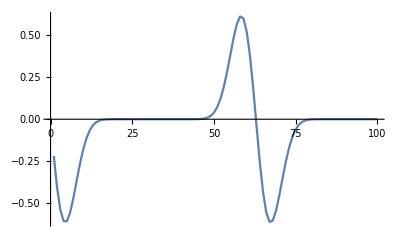

```mathematica
ListLinePlot[Im[ϕs[[2]]], PlotRange->All]
```

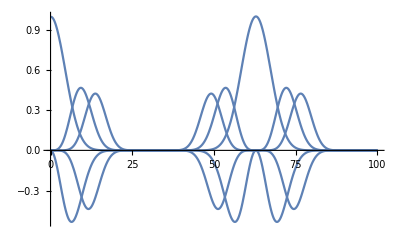

```mathematica
Plot[Table[Interpolation[ϕs[[2j-1]],Method->"Spline"][t],{j,1,5}],{t,0,100}, PlotRange->All]
```

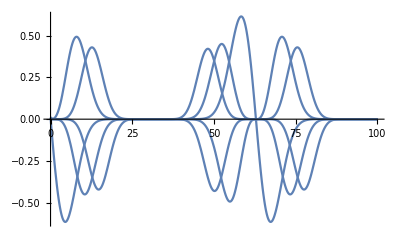

```mathematica
Plot[Table[Interpolation[Im[ϕs[[2j]]],Method->"Spline"][t],{j,1,5}],{t,0,100}, PlotRange->All]
```

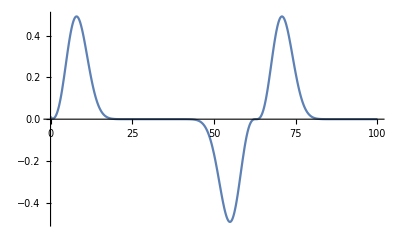

```mathematica
Plot[Interpolation[Im[ϕs[[4]]],Method->"Spline"][t],{t,0,100}, PlotRange->All]
```

```mathematica
Even=Table[Interpolation[Im[ϕs[[2j]]],Method->"Spline"][t],{j,1,5}];
```

```mathematica
DEven=Table[D[Even[[i]],t],{i,1,5}];
```

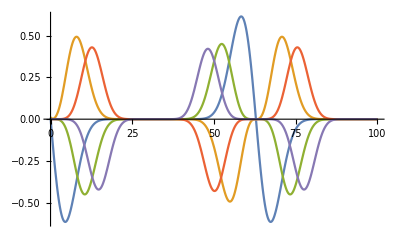

```mathematica
Plot[Even,{t,0,100}, PlotRange->All]
```

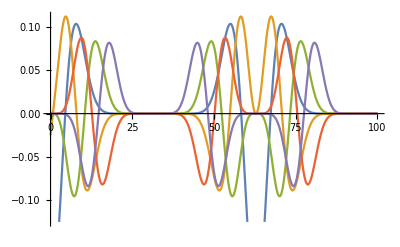

```mathematica
Plot[DEven,{t,0,100}]
```

```mathematica
DEvenTab=Table[{tVals[[i]],DEven[[1]]/.t->tVals[[i]]},{i,1,Length[tVals]}];
```

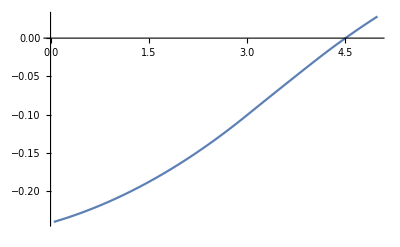

```mathematica
ListLinePlot[DEvenTab]
```

## Testing from saved files

```mathematica
Import["K_L7_cdMode3.m.gz"][[1;;3]]
```

{K_L7_cdMode3,bs length, precision: 355, 999.7.  Return Amplitude precision: 93.5837,tMax: 50  tPts: 500  Prec: 200}

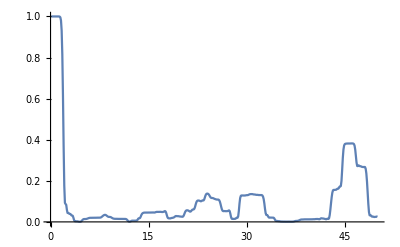

```mathematica
ListLinePlot[Import["K_L7_cdMode3.m.gz"][[5]], PlotRange->All]
```

```mathematica
Import["K_L7_4site_sp1234.m.gz"][[1;;3]]
```

{K_L7_4site_sp1234,bs length, precision: 691, 999.707.  Return Amplitude precision: 189.3,tMax: 50  tPts: 500  Prec: 200}

```mathematica
ACL7cd2=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_cdMode2.m"][[4]];
```

```mathematica
ACL7sp12=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_2site_sp12.m.gz"][[4]];
```

```mathematica
ACL7sp123=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_3site_sp123.m.gz"][[4]];
```

```mathematica
ACL7sp1234=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_4site_sp1234.m.gz"][[4]];
```

```mathematica
ACL7sp123[[3,5]]
```

-0.6366815632954266192516497985538088882589807415098878300373178753624505006478473052427788171883025184626898875473236965648275857476602025869467936491419815779932461392796534528818182797697667741265+0. ⅈ

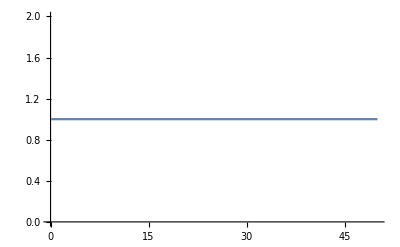

```mathematica
ListLinePlot[Table[{tVals[[j]],Sum[Abs[ACL7cd2[[k,j]]^2],{k,1,191}]},{j,1,Length[tVals]}]]
```

```mathematica
ListLinePlot[ParallelTable[{tVals[[j]],Range[392].Abs[ACL7cd2[[1;;392,j]]]^2},{j,1,Length[tVals]}, Method->"CoarsestGrained"], PlotRange->All]//EchoTiming
```

Part::take: Cannot take positions 1 through 392 in {{0.93161488226116686672097770485186104090652725695693371419308856363345282992145509319467593800593755745980089314007159954878245684090832874478495891481742079953903588312101567487300493960171455974547229 + 0. Power[10, -200] I, <<498>>, 0.0972329053008644623558630274044766<<146>>722579692462530007 + <<1>>}, <<190>>}.

```mathematica
ListLinePlot[Table[{tVals[[j]],Sum[Abs[ACL7sp1234[[k,j]]^2],{k,1,200}]},{j,1,Length[tVals]}], PlotRange->All]//EchoTiming
```

0.745451

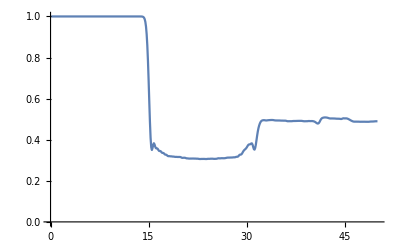

```mathematica
ListLinePlot[ParallelTable[{tVals[[j]],Sum[Abs[ACL7sp1234[[k,j]]^2],{k,1,200}]},{j,1,Length[tVals]}, Method->"CoarsestGrained"], PlotRange->All]//EchoTiming
```

0.155142

-Graphics-

```mathematica
ListLinePlot[ParallelTable[{tVals[[j]],Sum[(k-1)*Abs[ACL7sp1234[[k,j]]^2],{k,1,300}]},{j,1,Length[tVals]}, Method->"CoarsestGrained"], PlotRange->All]//EchoTiming
```

74.2036

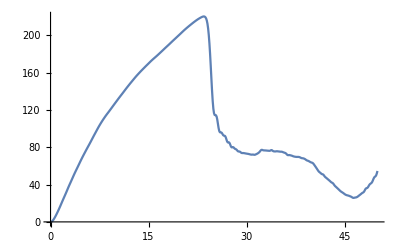

```mathematica
ListLinePlot[ParallelTable[{tVals[[j]],Total[Abs[ACL7sp1234[[1;;392,j]]]^2]},{j,1,Length[tVals]}, Method->"CoarsestGrained"], PlotRange->All]//EchoTiming
```

0.155169

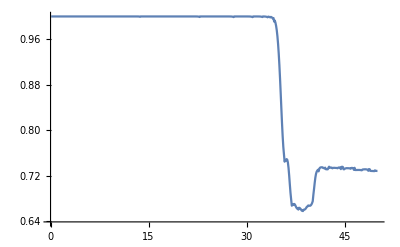

```mathematica
ListLinePlot[ParallelTable[{tVals[[j]],Range[392].Abs[ACL7sp1234[[1;;392,j]]]^2},{j,1,Length[tVals]}, Method->"CoarsestGrained"], PlotRange->All]//EchoTiming
```

0.179364

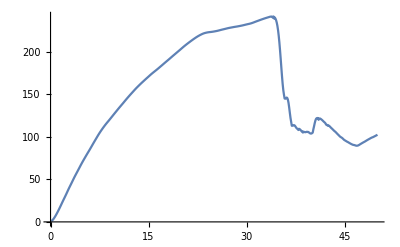

```mathematica
391-142
```

249

```mathematica
ListLinePlot[ParallelTable[{tVals[[j]],Sum[(k-1)*Abs[ACL7sp1234[[k,j]]^2],{k,100,349}]},{j,1,Length[tVals]}, Method->"FinestGrained"], PlotRange->All]//EchoTiming
```

$Aborted

```mathematica
list=RandomReal[1,10000000];
```

```mathematica
Sum[list[[i]],{i,1,250}]//EchoTiming
```

3.11107

123.427

```mathematica
Sum[list[[i]],{i,1,249}]//EchoTiming
```

0.0000837

122.657

```mathematica
Sum[list[[i]],{i,1,249}]+list[[250]]//EchoTiming
```

0.0000869

123.427

```mathematica
RepeatedTiming[Plus@@list[[1;;500]],5]
```

{0.0000386514,249.869}

```mathematica
RepeatedTiming[Total[list[[1;;500]]],5]
```

{9.67506×10^-7,249.869}

```mathematica
x=Table[i*list[[i]],{i,1,250}];//EchoTiming
```

1.08791

```mathematica
Total[x]//EchoTiming
```

8.×10^-6

15198.3

```mathematica
Sum[ACL7sp123[[k,4]],{k,1,250}]//EchoTiming
```

0.372552

1.739029725802173837576282098912235156740105923664413852130840420162520072466212554821463153093060760834850396351108942533447536875244847444385925591518342875458752211×10^113-4.1172342631436427641424155059086935974869086782087176184050617784645242958873067631978993536645918705987980445679575958440888281422721707332757292892183484336624559415×10^113 ⅈ

```mathematica
Range[Length[list[[1;;250]]]].list[[1;;250]]//EchoTiming
```

0.0000209

15198.3

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
EchoTiming[
Sum[ACL7sp123[[k,4]],{k,1,249}]+Abs[ACL7sp123[[250,4]]^2]]
```

0.0004265

1.569244238765963738495273498842755020852469304335393433055494286132104737471338405875138877134885890821777691796144302902537025822576670493483234336391662628357035077×10^227-1.558655113534692437212209686404403966740926317817566254195606738953424896056048764588016963146321293747899549197144230220863857834194490099157777712948755361879528801×10^112 ⅈ

```mathematica
Table[Sum[(k-1)*Abs[ACL7sp123[[k,j]]^2],{k,100,349}],{j,1,Length[tVals]}];//EchoTiming
```

$Aborted

```mathematica
Table[Sum[(k-1)*Abs[ACL7sp123[[k,4]]^2],{k,100,349}],{j,1,Length[tVals]}]//EchoTiming
```

$Aborted

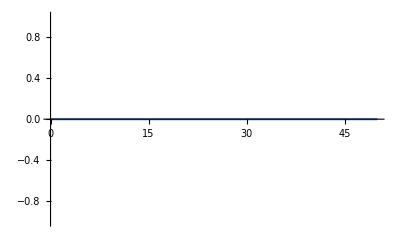

```mathematica
ListLinePlot[Import["K_L7_2site_sp12.m.gz"][[4]]]
```

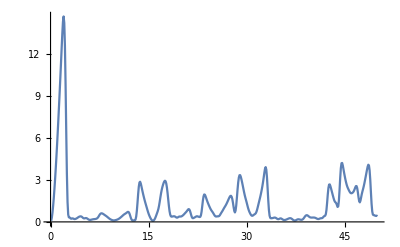

```mathematica
ListLinePlot[Import["K_L7_2site_sp12.m.gz"][[4]], PlotRange->All]
```